## Useful functions

```mathematica
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->12,Magnification->1.6};
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

Get::noopen: Cannot open MaTeX`.

$Failed

C:\Users\conte\Desktop\Repository\31_resonances\code

```mathematica
RiccatiBesselJ[z_,l_]:=z SphericalBesselJ[l,z];
RiccatiBesselN[z_,l_]:=z SphericalBesselY[l,z];
```

```mathematica
(*Boundery conditions for the wavefunction*)
alpha[ra_,ka_,la_,ha_]:=RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]

beta[rb_,kb_,lb_,hb_]:=RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])
```

LEC=(Λ,a_(3-1)^(S-wave) [fm],C_(2-body) [MeV],C_(3-body) [MeV])
the triton-proton S-wave scattering length is used to calibrate the core parameter and
was obtained by R. Lazauskas.

```mathematica
(* Nuclear E2=2.22 E3=8.48 ℏc=198*)
(* λ a0,r0 (Martin, 23) a1,r1 (Martin,45) a0 (Rimas, unprojected, 6) a1 (Rimas, unprojected, 7) a0 (Rimas, projected, 8) a1 (Rimas, projected, 9)*)
a0a1NUCLmartinrimas=Import[NotebookDirectory[]<>"../data/a0-a1_nucl_Rimas-Martin.dat","Table"][[2;;]];
(* λ C0,D0 (Martin, 23) C0,D0 (Rimas, unprojected, 45) C0,Do (Rimas, projected, 67)*)
LECsNUCLmartinrimas=Import[NotebookDirectory[]<>"../data/LECs_nucl_Rimas-Martin.dat","Table"][[2;;]];

activeLEC=LECsNUCLmartinrimas[[All,{1,6,7}]];
a0a1REFERENCE=a0a1NUCLmartinrimas[[All,{8,9}]];
```

(non)local resonating-group potentials from a 2- and 3-body contact interaction for TRIMER-FERMION (ABC-A)

W_(non-local) takes the Energy (e_) in [MeV]

```mathematica
NormTF[core_?ArrayQ]:=1./Sqrt[Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]] (Pi/(core[[i]][[2]]+core[[j]][[2]]))^1.5,{i,Length[core]},{j,Length[core]}]]]];

VlocTF[r_,lam_,Cc_,Dd_,Aa_,Bb_]:=Block[{eta2,eta3,w2,w3},
eta2=2. Cc/(2. (Aa+Bb)(3. Aa+3. Bb+2. lam))^(3./2.);
w2=3. (Aa+Bb) lam/(3. (Aa+Bb)+2. lam);
eta3=Dd/(6. (Aa+Bb)^2+16. (Aa+Bb) lam+2. lam^2)^(3./2.);
w3=(3. (Aa+Bb) lam ((Aa+Bb)+2. lam)/(3. (Aa+Bb)^2+8. (Aa+Bb) lam+lam^2));
eta2 Exp[-w2 r^2]+eta3  Exp[-w3 r^2]
];

WnolocTF[r_,rp_,Ee_,lam_,Cc_,Dd_,Aa_,Bb_,Ll_,TwoMyOverHBsq_]:=Block[{zeta1,zeta2,zeta3,a1,b1,c1,a2,b2,c2,a3,b3,c3},
zeta1=(27./64.)(2 (Aa+Bb))^(-3./2.) (1./TwoMyOverHBsq);
a1=(Aa+9. Bb) 3./32.;
b1=(Aa+Bb) 9./16.;
c1=(9. Aa+Bb) 3./32.;

zeta2=-27./32. Cc/(2. (Aa+Bb)+lam)^(3./2.);
zeta3=-27./64. Dd/(2  (Aa+Bb)+5 lam)^(3./2.);

a2=3. (Aa^2+9. Bb^2+10. Aa Bb+(14. Aa+18. Bb) lam)/(16. (2. (Aa+Bb)+lam));
b2=18. (Aa+Bb) ((Aa+Bb)+2. lam)/(16. (2. (Aa+Bb)+lam));
c2=3. (9. Aa^2+Bb^2+10. Aa Bb+(6. Aa+2. Bb) lam)/(16. (2. (Aa+Bb)+lam));

a3=3. (Aa^2+9. Bb^2+10. Aa Bb+(16. Aa+36. Bb) lam+27. lam^2)/(16. (2. (Aa+Bb)+5. lam));
b3=18. ((Aa+Bb)^2+4. (Aa+Bb) lam+3. lam^2)/(16. (2. (Aa+Bb)+5. lam));
c3=3. (9. Aa^2+Bb^2+10. Aa Bb+(24. Aa+4. Bb) lam+3. lam^2)/(16. (2 (Aa+Bb)+5. lam));

-(4 Pi r rp) (
zeta1 Exp[-a1 (r^2+rp^2)] ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)+(Ll+1) Ll/r^2-TwoMyOverHBsq Ee) I^Ll  SphericalBesselJ[Ll,I b1 r rp]
-4 a1 b1 r rp Sum[(1-Ll^2+l^2) I^(l+1)/Sqrt[3] (2/Sqrt[5])^((Ll+l)/2) SphericalBesselJ[1+l,I b1 r rp],{l,-Ll,Ll}])
+I^Ll zeta2 SphericalBesselJ[Ll,I b2 r rp] Exp[-a2 r^2-c2 rp^2]
+I^Ll zeta3 SphericalBesselJ[Ll,I b3 r rp] Exp[-a3 r^2-c3 rp^2]
)
];
```

The function <SolveSecular> expects the variable <<momentum>> in  [fm^-1]
As  W_(non-local) takes the Energy (e_) in [MeV];
The core wave function is parametrized via the "a0={{c_1,α_1},{c_2,α_2},...,{c_N,α_N}}" array:
ϕ_core=(∑^N)_(i=1)c_i·e_^(-α_i/2∏_j (r^-)_j^2)

```mathematica
SolveSecular[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},

hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Amat=ConstantArray[0,{Npoints,Npoints}];

normsqu=NormTF[a00]^2;

matContainer={};

Do[
If[a00[[ii]][[1]] a00[[jj]][[1]]≠0,

cij=a00[[ii]][[1]] a00[[jj]][[1]] normsqu;


amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]]],{i,1,Npoints}]];
wmat=Table[-hDif^3 TwoMyOverHBsq WnolocTF[i hDif,j hDif,energyMeV,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],Lin,TwoMyOverHBsq],{i,1,Npoints},{j,1,Npoints}]; 

AppendTo[matContainer,cij (amat+wmat)];

]
,{ii,1,Length[a00]},{jj,1,Length[a00]}];

Amat=Plus[matContainer[[1]]];

Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];

Amat+=(Kmat+Dmat);

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);

tanDelta
]
```

```mathematica
SolveSecularF[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,c01_?NumberQ,a01_?NumberQ,c02_?NumberQ,a02_?NumberQ,TwoMyOverHBsq_?NumberQ]:=Block[{a00,hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},

hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Amat=ConstantArray[0,{Npoints,Npoints}];

a00={{c01,a01},{c02,a02}};

normsqu=NormTF[a00]^2;

Do[
If[a00[[ii]][[1]] a00[[jj]][[1]]≠0,

cij=a00[[ii]][[1]] a00[[jj]][[1]] normsqu;


amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]]],{i,1,Npoints}]];
wmat=Table[-hDif^3 TwoMyOverHBsq WnolocTF[i hDif,j hDif,energyMeV,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],Lin,TwoMyOverHBsq],{i,1,Npoints},{j,1,Npoints}]; 

Amat+=(cij (amat+wmat));

]
,{ii,1,Length[a00]},{jj,1,Length[a00]}];

Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];

Amat+=(Kmat+Dmat);

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);

tanDelta
]
```

numerical and physical parameters

```mathematica
nGrid=200;

nf={6,4}; (* number form for printing, only *)
k0FM=0.1;  (*initial momentum*)

rr=25.0;   (*Integration radius*)
αL=Get[LocalObject["3-1_CorePara_SwaveRimas"]]; (*what was the old αL for rimas*)

hbar=197.327053;
Mm=938.92;
m1=3 Mm;m2=Mm;
μ=m1 m2/(m1+m2);mh2=(2 μ)/(hbar)^2;
Print["E_0 = ",(k0FM hbar)^2/(2 μ)," MeV"]
λRange=Range[1,Length[activeLEC]];
```

LocalObject::nso: LocalObject[file:///C:/Users/conte/AppData/Roaming/Wolfram/Objects/3-1_CorePara_SwaveRimas] not found.

E_0 = 0.276473 MeV

```mathematica
findLogDivisions[{xmin_,xmax_},n_Integer]:=10^FindDivisions[Log10@{xmin,xmax},n]

GetERE[x_]:=Module[{localcore=x},

core=localcore;

dataS={};dataP={};
tanDsL={};tanDpL={};
tanDs={};tanDp={};

Do[
momFM=Sqrt[2 μ energ]/hbar;
TanDelSwave=Chop[SolveSecular[rr,nGrid,momFM,0,λ,C0,D0,core,mh2]];
TanDelPwave=Chop[SolveSecular[rr,nGrid,momFM,1,λ,C0,D0,core,mh2]];
AppendTo[tanDs,{energ,TanDelSwave}];
AppendTo[tanDp,{energ,TanDelPwave}];
,{energ,ErangeMeV}];

tanDs=Reverse[Sort[tanDs,#1[[1]]>#2[[1]]&]]; (*Sort all the momentum since it is parallel*)
tanDp=Reverse[Sort[tanDp,#1[[1]]>#2[[1]]&]]; (*Sort all the momentum since it is parallel*)
(*AppendTo[tanDsL,tnDs];
AppendTo[tanDpL,tnDp];*)
(*Extract the ERE Parameters*)
Lrel = 0;
dataS=Transpose[{(Sqrt[2 μ ErangeMeV]/hbar),(Sqrt[2 μ ErangeMeV]/hbar)/Re[tanDs⟦All,2⟧]}];
EreS=Fit[dataS⟦f1;;f2⟧,{1,p^2},p];
a0tf=-Coefficient[EreS,p,0]^-1;
r0tf= Coefficient[EreS,p,2]*2.;
Lrel = 1;
dataP=Transpose[{(Sqrt[2 μ ErangeMeV]/hbar),(Sqrt[2 μ ErangeMeV]/hbar)^3/tanDp⟦All,2⟧}];
EreP=Fit[dataP⟦f1;;f2⟧,{1,p^2},p];
a1tf=-Coefficient[EreP,p,0]^-1;
r1tf= Coefficient[EreP,p,2]*2.;
Print["dataS = ", dataS];
{a0tf,r0tf,a1tf,r1tf}
]
```

```mathematica
PlotERE:=Module[{},(*Plot the Phaseshifts for each α and C that I used*)
phaseS=Table[Transpose[{tanDs⟦i,1⟧, ArcTan[tanDs⟦i,2⟧]}],{i,1,Length[tanDs⟦All,1⟧]}];
phaseP=Table[Transpose[{tanDp⟦i,1⟧, ArcTan[tanDp⟦i,2⟧]}],{i,1,Length[tanDp⟦All,1⟧]}];
(*---------*)
Tfits=(Fit[dataS⟦1;;Min[10,Length[dataS]]⟧,{1,p^2,p^4},p]); (*fit ere again*)
dataTS=dataS;dataTS⟦All,2⟧=dataTS⟦All,2⟧^-1 ;
Polesp=(p/.NSolve[Tfits-ⅈ p==0,{p}]) ; (*find pole positions*) PolesE=hbar^2 Polesp^2 / (2 μ);
Print["S Pole Poitions in momentum: ", Polesp];
Print["S Pole Poitions in energy:   ", PolesE];
(*---------*)
Tfitp=(Fit[dataP⟦1;;Min[10,Length[dataP]]⟧,{1,p^2,p^4},p]); (*fit ere again*)
dataTP=dataP;dataTP⟦All,2⟧=dataTP⟦All,2⟧^-1 ;
Polepp=(p/.NSolve[Tfitp-ⅈ p^3==0,{p}]) ; (*find pole positions*) PolepE=hbar^2 Polepp^2 / (2 μ);
Print["P Pole Poitions in momentum: ", Polepp];
Print["P Pole Poitions in energy:   ", PolepE];


GraphicsGrid[{{
Show[{ Plot[-(1/a0tf)+(1/2)r0tf k^2,{k,0,dataS⟦-1,1⟧}],ListPlot[dataS,PlotRange->{{dataS⟦1,1⟧,dataS⟦1,-1⟧},All}]},ImageSize->500,AxesLabel->{"E [MeV]","K CotTan[δ_(S - wave)] [fm^-1]"},PlotStyle->"Red", PlotLabel->" S-wave KCotδ compared with -1/a0+1/2r0 k^2"]
,
Show[{ Plot[-(1/a1tf)+(1/2)r1tf k^2,{k,0,dataP⟦-1,1⟧}],ListPlot[dataP,PlotRange->{{dataP⟦1,1⟧,dataP⟦1,-1⟧},All}]},ImageSize->500,AxesLabel->{"E [MeV]","K^3 CotTan[δ_(S - wave)] [fm^-3]"},PlotStyle->"Red",PlotLabel->" P-wave K^3Cotδ compared with -1/a0+1/2r0 k^2"]

},
{
Show[ListPlot[dataTS],Plot[Tfits^-1,{p,0,0.4},PlotRange->{Automatic,Automatic}],ImageSize->500,PlotLabel->"T matrix compared with the ERE^-1(O(k^4)) expansion"],
Show[ListPlot[dataTP],Plot[Tfitp^-1,{p,0,0.4},PlotRange->{Automatic,Automatic}],ImageSize->500,PlotLabel->"T matrix compared with the ERE^-1(O(k^4)) expansion"]

}
},ImageSize->1000]]
```

## Import density and fit wavefunctions

```mathematica
Martinϕ1=Cases[Import["..\data/abc_u_1.0_binf_r1b.dnst","Table"],{_?NumberQ,___}];
Mϕ1=Transpose[{Martinϕ1⟦All,1⟧,Sqrt[Martinϕ1⟦All,3⟧]}];
Jϕ1=Import["..\data\abc_u_1.0_J.dat","Table"];Jϕ1⟦All,2⟧=Jϕ1⟦All,2⟧ Mϕ1⟦1,2⟧/Jϕ1⟦1,2⟧;
Martinϕ2=Cases[Import["..\data/abc_u_2.0_binf_r1b.dnst","Table"],{_?NumberQ,___}];
Mϕ2=Transpose[{Martinϕ2⟦All,1⟧,Sqrt[Martinϕ2⟦All,3⟧]}];
Martinϕ3=Cases[Import["..\data/abc_u_3.0_binf_r1b.dnst","Table"],{_?NumberQ,___}];
Mϕ3=Transpose[{Martinϕ3⟦All,1⟧,Sqrt[Martinϕ3⟦All,3⟧]}];
Martinϕ4=Cases[Import["..\data/abc_u_4.0_binf_r1b.dnst","Table"],{_?NumberQ,___}];
Mϕ4=Transpose[{Martinϕ4⟦All,1⟧,Sqrt[Martinϕ4⟦All,3⟧]}];
Martinϕ6=Cases[Import["..\data/abc_u_6.0_binf_r1b.dnst","Table"],{_?NumberQ,___}];
Mϕ6=Transpose[{Martinϕ6⟦All,1⟧,Sqrt[Martinϕ6⟦All,3⟧]}];
Martinϕ8=Cases[Import["..\data/abc_u_8.0_binf_r1b.dnst","Table"],{_?NumberQ,___}];
Mϕ8=Transpose[{Martinϕ8⟦All,1⟧,Sqrt[Martinϕ8⟦All,3⟧]}];
Martinϕ10=Cases[Import["..\data/abc_u_10.0_binf_r1b.dnst","Table"],{_?NumberQ,___}];
Mϕ10=Transpose[{Martinϕ10⟦All,1⟧,Sqrt[Martinϕ10⟦All,3⟧]}];
```

```mathematica
nk=3;
core={}; Do[core=AppendTo[core,ToExpression@Map[StringJoin[#,ToString[k]]&,{"C","Α"}]],{k,1,nk}];
wf=Total[Flatten[Table[core⟦i⟧⟦1⟧ⅇ^(-core⟦i⟧⟦2⟧ r^2) ,{i,Length[core]}]]];
(* Preliminary easy fit for starting point*)
core4=core/.FindFit[Mϕ4,wf,Flatten[core],r];
corefit=Transpose[{Flatten[core],Flatten[core4]}];




core1=core/.FindFit[Mϕ1,wf,corefit,r]; 
wf1    =Total[Flatten[Table[core1⟦i⟧⟦1⟧ⅇ^(-core1⟦i⟧⟦2⟧ r^2) ,{i,Length[core1]}]]];
core2=core/.FindFit[Mϕ2,wf,corefit,r]; 
wf2    =Total[Flatten[Table[core2⟦i⟧⟦1⟧ⅇ^(-core2⟦i⟧⟦2⟧ r^2) ,{i,Length[core2]}]]];
core3=core/.FindFit[Mϕ3,wf,corefit,r]; 
wf3    =Total[Flatten[Table[core3⟦i⟧⟦1⟧ⅇ^(-core3⟦i⟧⟦2⟧ r^2) ,{i,Length[core3]}]]];
core4=core/.FindFit[Mϕ4,wf,corefit,r];
wf4    =Total[Flatten[Table[core4⟦i⟧⟦1⟧ⅇ^(-core4⟦i⟧⟦2⟧ r^2) ,{i,Length[core4]}]]];
core6=core/.FindFit[Mϕ6,wf,corefit,r];
wf6    =Total[Flatten[Table[core6⟦i⟧⟦1⟧ⅇ^(-core6⟦i⟧⟦2⟧ r^2) ,{i,Length[core6]}]]];
core8=core/.FindFit[Mϕ8,wf,corefit,r]; 
wf8    =Total[Flatten[Table[core8⟦i⟧⟦1⟧ⅇ^(-core8⟦i⟧⟦2⟧ r^2) ,{i,Length[core8]}]]];
core10=core/.FindFit[Mϕ10,wf,corefit,r]; 
wf10    =Total[Flatten[Table[core10⟦i⟧⟦1⟧ⅇ^(-core10⟦i⟧⟦2⟧ r^2) ,{i,Length[core10]}]]];
Print["wf1 = ", wf1]
Print["wf2 = ", wf2]
Print["wf3 = ", wf3]
Print["wf4 = ", wf4]
Print["wf6 = ", wf6]
Print["wf8 = ", wf8]
Print["wf10 = ", wf10]
```

wf1 = 0.106373 ⅇ^(-0.371415 r^2)-1.36285 ⅇ^(-0.102385 r^2)+1.40205 ⅇ^(-0.102385 r^2)

wf2 = 0.159045 ⅇ^(-0.662473 r^2)+1.58368 ⅇ^(-0.140094 r^2)-1.53 ⅇ^(-0.140094 r^2)

wf3 = 0.189254 ⅇ^(-0.873276 r^2)-1.35096 ⅇ^(-0.162914 r^2)+1.41418 ⅇ^(-0.162914 r^2)

wf4 = 0.208715 ⅇ^(-1.03031 r^2)-1.34759 ⅇ^(-0.178617 r^2)+1.41757 ⅇ^(-0.178617 r^2)

wf6 = 0.232307 ⅇ^(-1.24303 r^2)+1.24292 ⅇ^(-0.198532 r^2)-1.16434 ⅇ^(-0.198532 r^2)

wf8 = 0.24585 ⅇ^(-1.37572 r^2)+1.22839 ⅇ^(-0.210204 r^2)-1.14476 ⅇ^(-0.210204 r^2)

wf10 = 0.257821 ⅇ^(-1.49207 r^2)+1.21622 ⅇ^(-0.221642 r^2)-1.12811 ⅇ^(-0.221642 r^2)

```mathematica
GraphicsGrid[{{
Show[ListPlot[{Mϕ1,Jϕ1},PlotRange->All,PlotStyle->{Gray,Blue}],Plot[wf1,{r,-1,10},PlotStyle->{Orange,Thick}],ImageSize->500, AxesLabel->{"WaveFunction","r [fm]"},PlotLabel->"Λ = 1 fm^-1"],
Show[ListPlot[Mϕ2,PlotRange->All,PlotStyle->Gray],Plot[wf2,{r,-1,10},PlotStyle->{Orange,Thick}],ImageSize->500, AxesLabel->{"WaveFunction","r [fm]"},PlotLabel->"Λ = 2 fm^-1"]},
{
Show[ListPlot[Mϕ3,PlotRange->All,PlotStyle->Gray],Plot[wf3,{r,-1,10},PlotStyle->{Orange,Thick}],ImageSize->500, AxesLabel->{"WaveFunction","r [fm]"},PlotLabel->"Λ = 3 fm^-1"],
Show[ListPlot[Mϕ4,PlotRange->All,PlotStyle->Gray],Plot[wf4,{r,-1,10},PlotStyle->{Orange,Thick}],ImageSize->500, AxesLabel->{"WaveFunction","r [fm]"},PlotLabel->"Λ = 4 fm^-1" ]},
{
Show[ListPlot[Mϕ6,PlotRange->All,PlotStyle->Gray],Plot[wf6,{r,-1,10},PlotStyle->{Orange,Thick}],ImageSize->500, AxesLabel->{"WaveFunction","r [fm]"},PlotLabel->"Λ = 6 fm^-1"],
Show[ListPlot[Mϕ8,PlotRange->All,PlotStyle->Gray],Plot[wf8,{r,-1,10},PlotStyle->{Orange,Thick}],ImageSize->500, AxesLabel->{"WaveFunction","r [fm]"},PlotLabel->"Λ = 8 fm^-1" ]},
{
Show[ListPlot[Mϕ10,PlotRange->All,PlotStyle->Gray],Plot[wf10,{r,-1,10},PlotStyle->{Orange,Thick}],ImageSize->500, AxesLabel->{"WaveFunction","r [fm]"},PlotLabel->"Λ = 10 fm^-1"],
ListPlot[{Mϕ1,Mϕ2,Mϕ3,Mϕ4,Mϕ6,Mϕ8,Mϕ10},PlotRange->All,Joined->True,ImageSize->400,PlotRange->Full,PlotLegends->{"Λ = 1 fm^-1","Λ = 2 fm^-1","Λ = 3 fm^-1","Λ = 4 fm^-1","Λ = 6 fm^-1","Λ = 8 fm^-1","Λ = 10 fm^-1"}]}
},ImageSize->1000]
```

-Graphics-

## Testing The method with different parameters (λ=4 fm^-1)

## Fast (Rmax = 10, Ngrid=20)

λ = Λ^2/4 = 4.0000  ⇒ Λ = 4.0000 ; C_0 = -505.1500 ; D_0 = 1426.7500

Core = {{-1.34759,0.178617},{0.208715,1.03031},{1.41757,0.178617}}

ERE =      a0 = 9.9999     r0 = 6.68719     a1 = 333.323     r1 = -0.358105

S Pole Poitions in momentum: {-0.149493+0.151496 ⅈ,0.+0.186808 ⅈ,0.-0.489801 ⅈ,0.149493+0.151496 ⅈ}

S Pole Poitions in energy:   {-0.0166674-1.25229 ⅈ,-0.96482+0. ⅈ,-6.63273+0. ⅈ,-0.0166674+1.25229 ⅈ}

P Pole Poitions in momentum: {-0.182964+0.177209 ⅈ,0.-0.0998396 ⅈ,0.+0.219621 ⅈ,0.182964+0.177209 ⅈ}

P Pole Poitions in energy:   {0.0573055-1.79281 ⅈ,-0.275587+0. ⅈ,-1.33352+0. ⅈ,0.0573055+1.79281 ⅈ}

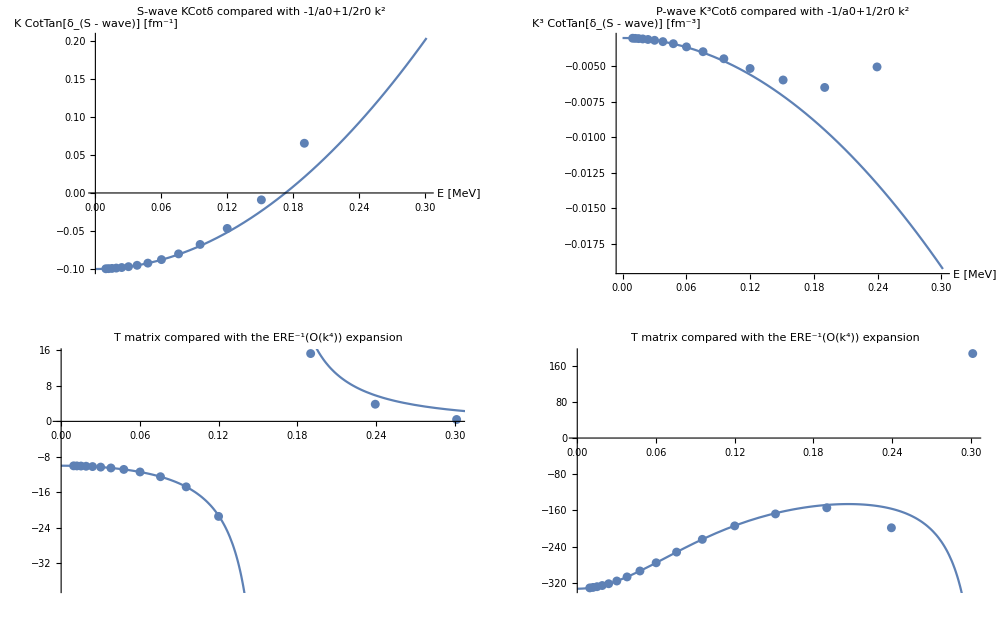

```mathematica
λλ=4;
mycore=core4;
rr=10;nGrid=20;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.01;
k0FMax=0.3;
Divisions=20;



(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;

(*---------------------*)
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2/4 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];
Print["Core = ",mycore]
ERE=GetERE[mycore];
Print["ERE = ","     a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧]
PlotERE
```

## Medium (Rmax = 10, Ngrid=100)

λ = Λ^2/4 = 4.0000  ⇒ Λ = 4.0000 ; C_0 = -505.1500 ; D_0 = 1426.7500

Core = {{-1.34759,0.178617},{0.208715,1.03031},{1.41757,0.178617}}

ERE =      a0 = 9.99173     r0 = 6.68169     a1 = 332.259     r1 = -0.358492

S Pole Poitions in momentum: {-0.14961+0.151628 ⅈ,0.+0.186973 ⅈ,0.-0.490229 ⅈ,0.14961+0.151628 ⅈ}

S Pole Poitions in energy:   {-0.0168032-1.25437 ⅈ,-0.966521+0. ⅈ,-6.64433+0. ⅈ,-0.0168032+1.25437 ⅈ}

P Pole Poitions in momentum: {-0.183152+0.177406 ⅈ,0.-0.0999462 ⅈ,0.+0.219867 ⅈ,0.183152+0.177406 ⅈ}

P Pole Poitions in energy:   {0.0572815-1.79664 ⅈ,-0.276176+0. ⅈ,-1.33651+0. ⅈ,0.0572815+1.79664 ⅈ}

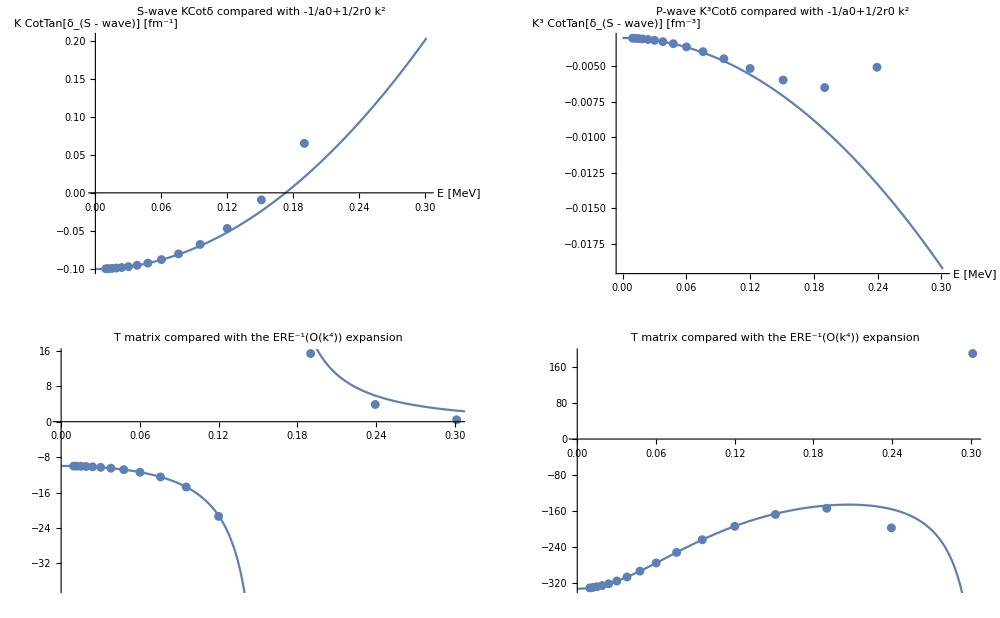

```mathematica
λλ=4;
mycore=core4;
rr=10;nGrid=100;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.01;
k0FMax=0.3;
Divisions=20;



(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;

(*---------------------*)
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];
Print["Core = ",mycore]
ERE=GetERE[mycore];
Print["ERE = ","     a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧]
PlotERE
```

## Double grid (Rmax = 10, Ngrid=200)

λ = Λ^2 = 4.0000  ⇒ Λ = 4.0000 ; C_0 = -505.1500 ; D_0 = 1426.7500

Core = {{-1.34759,0.178617},{0.208715,1.03031},{1.41757,0.178617}}

ERE =      a0 = 9.98085     r0 = 6.67437     a1 = 331.065     r1 = -0.358927

S Pole Poitions in momentum: {-0.149767+0.151804 ⅈ,0.+0.187192 ⅈ,0.-0.4908 ⅈ,0.149767+0.151804 ⅈ}

S Pole Poitions in energy:   {-0.0169845-1.25713 ⅈ,-0.96879+0. ⅈ,-6.65981+0. ⅈ,-0.0169845+1.25713 ⅈ}

P Pole Poitions in momentum: {-0.183364+0.177626 ⅈ,0.-0.100066 ⅈ,0.+0.220144 ⅈ,0.183364+0.177626 ⅈ}

P Pole Poitions in energy:   {0.0572587-1.80096 ⅈ,-0.276841+0. ⅈ,-1.33989+0. ⅈ,0.0572587+1.80096 ⅈ}

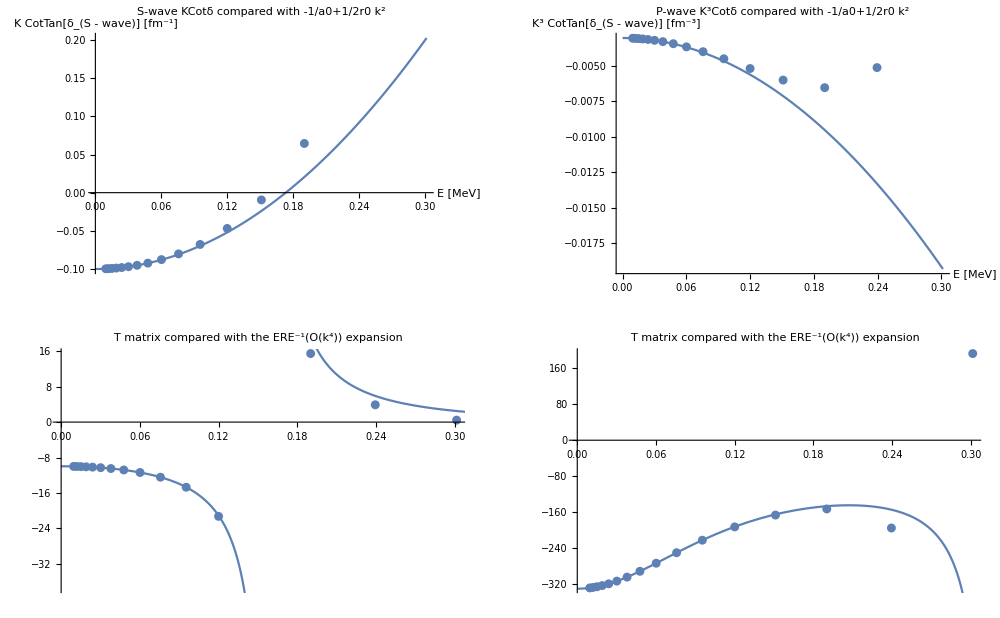

```mathematica
λλ=4;
mycore=core4;
rr=10;nGrid=200;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.01;
k0FMax=0.3;
Divisions=20;



(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;

(*---------------------*)
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];
Print["Core = ",mycore]
ERE=GetERE[mycore];
Print["ERE = ","     a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧]
PlotERE
```

## Long (Rmax = 15, Ngrid=200)

λ = Λ^2/4 = 4.0000  ⇒ Λ = 4.0000 ; C_0 = -505.1500 ; D_0 = 1426.7500

Core = {{-1.34759,0.178617},{0.208715,1.03031},{1.41757,0.178617}}

ERE =      a0 = 14.9993+1.62654×10^-8 ⅈ     r0 = 10.0695-2.90318×10^-7 ⅈ     a1 = 1124.84-0.000995067 ⅈ     r1 = -0.237164+1.15381×10^-6 ⅈ

S Pole Poitions in momentum: {-0.102248+0.0968534 ⅈ,-4.02889×10^-9-0.312198 ⅈ,2.01562×10^-9+0.118491 ⅈ,0.102248+0.0968534 ⅈ}

S Pole Poitions in energy:   {0.0296956-0.547587 ⅈ,-2.69472+6.95503×10^-8 ⅈ,-0.388173+1.32062×10^-8 ⅈ,0.0296956+0.547587 ⅈ}

P Pole Poitions in momentum: {-0.124767+0.115422 ⅈ,-2.384×10^-6+0.141707 ⅈ,1.55982×10^-7-0.0664559 ⅈ,0.124766+0.11542 ⅈ}

P Pole Poitions in energy:   {0.0620516-0.79629 ⅈ,-0.555183-0.0000186802 ⅈ,-0.122101-5.7318×10^-7 ⅈ,0.0620611+0.796269 ⅈ}

ListPlot::prng: Value of option PlotRange -> {{0.00953176,-0.0662118+7.13868×10^-11 ⅈ},All} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

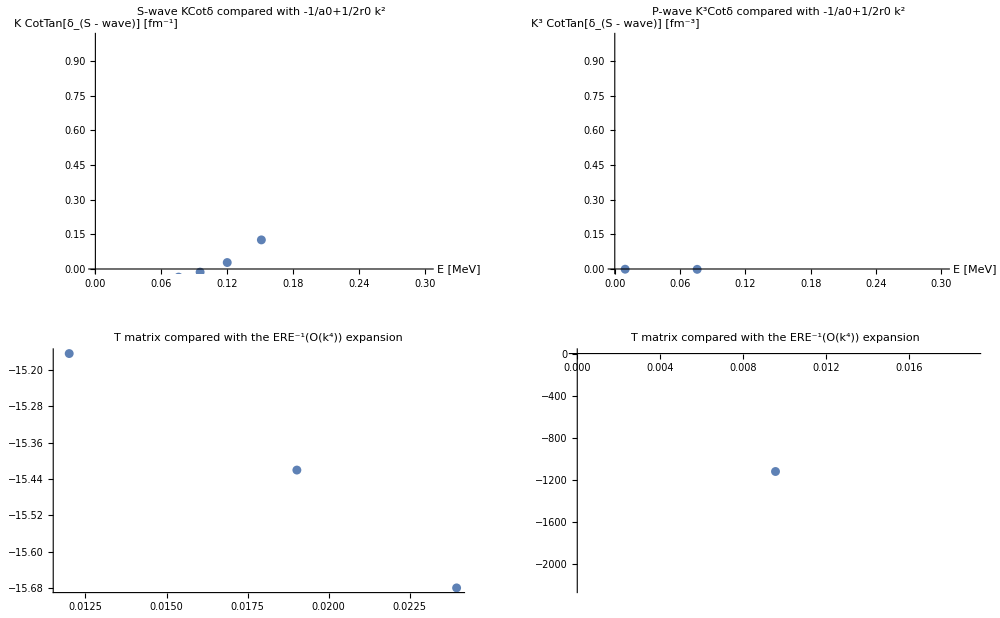

```mathematica
λλ=4;
mycore=core4;
rr=15;nGrid=200;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.01;
k0FMax=0.3;
Divisions=20;



(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;

(*---------------------*)
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2/4 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];
Print["Core = ",mycore]
ERE=GetERE[mycore];
Print["ERE = ","     a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧]
PlotERE
```

## Test dynamical (Rmax = 50, Ngrid=100)

λ = Λ^2/4 = 4.0000  ⇒ Λ = 4.0000 ; C_0 = -505.1500 ; D_0 = 1426.7500

Core = {{-1.34759,0.178617},{0.208715,1.03031},{1.41757,0.178617}}

dataS = {{0.00953176,-0.0186865},{0.0119998,-0.017791},{0.0151068,-0.0161401},{0.0190184,-0.0135873},{0.0239427,-0.00968558},{0.0301421,-0.00238711},{0.0379466,0.0120437},{0.047772,0.0492191},{0.0601414,0.358945},{0.0757135,-0.109218},{0.0953176,-0.000424362},{0.119998,0.333448},{0.151068,-0.0595508},{0.190184,2.58169},{0.239427,0.273111},{0.301421,0.158455}}

ERE =      a0 = 48.8734     r0 = 37.9244     a1 = 38776.5-0.000643462 ⅈ     r1 = -0.0653405+3.31177×10^-9 ⅈ

S Pole Poitions in momentum: {-0.0736631-0.00358984 ⅈ,-0.0223721+0.00358984 ⅈ,0.0223721+0.00358984 ⅈ,0.0736631-0.00358984 ⅈ}

S Pole Poitions in energy:   {0.149665+0.014622 ⅈ,0.0134815-0.00444084 ⅈ,0.0134815+0.00444084 ⅈ,0.149665-0.014622 ⅈ}

P Pole Poitions in momentum: {-0.0526332+0.0161321 ⅈ,-3.1731×10^-10+0.0103904 ⅈ,2.50012×10^-10-0.00935546 ⅈ,0.0526332+0.0161321 ⅈ}

P Pole Poitions in energy:   {0.069395-0.0469497 ⅈ,-0.00298481-1.82305×10^-10 ⅈ,-0.00241983-1.29333×10^-10 ⅈ,0.069395+0.0469497 ⅈ}

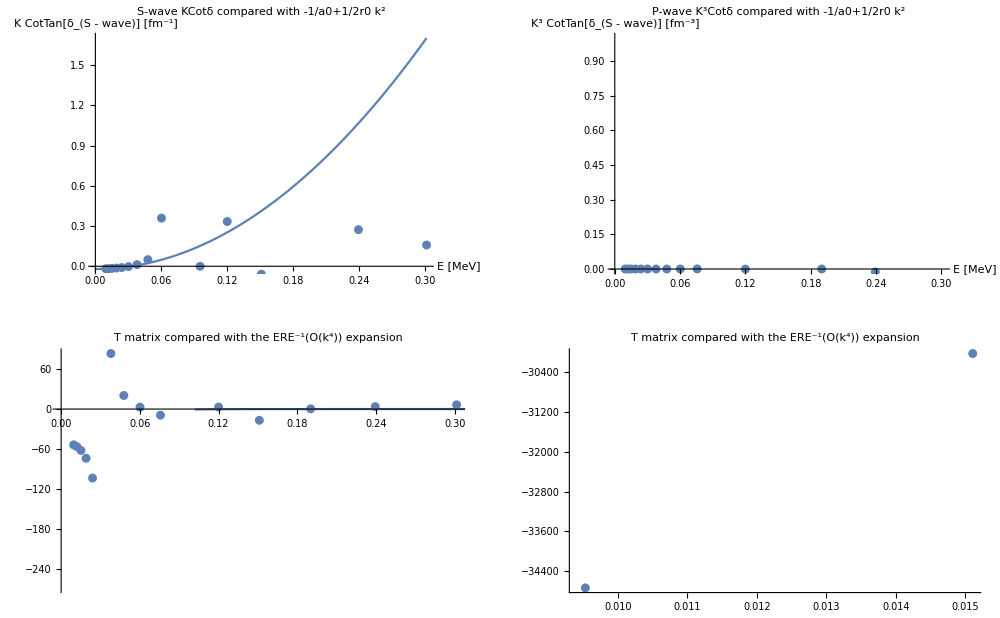

```mathematica
λλ=4;
mycore=core4;
rr=200;nGrid=200;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.01;
k0FMax=0.3;
Divisions=20;



(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;

(*---------------------*)
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2/4 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];
Print["Core = ",mycore]
ERE=GetERE[mycore];
Print["ERE = ","     a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧]
PlotERE
```

## Calculate all the cut-off

λ = Λ^2/4 = 0.2500  ⇒ Λ = 1.0000 ; C_0 = -44.4515 ; D_0 = 27.2450

Core = {{-1.36285,0.102385},{0.106373,0.371415},{1.40205,0.102385}}

ERE =      a0 = 9.99173     r0 = 6.68169     a1 = 332.259     r1 = -0.358492

S Pole Poitions in momentum: {-0.157133+0.160074 ⅈ,0.+0.197508 ⅈ,0.-0.517656 ⅈ,0.157133+0.160074 ⅈ}

S Pole Poitions in energy:   {-0.0257886-1.39082 ⅈ,-1.07851+0. ⅈ,-7.40859+0. ⅈ,-0.0257886+1.39082 ⅈ}

P Pole Poitions in momentum: {-0.197812+0.193642 ⅈ,0.-0.108305 ⅈ,0.+0.239288 ⅈ,0.197812+0.193642 ⅈ}

P Pole Poitions in energy:   {0.0451357-2.11805 ⅈ,-0.3243+0. ⅈ,-1.58305+0. ⅈ,0.0451357+2.11805 ⅈ}

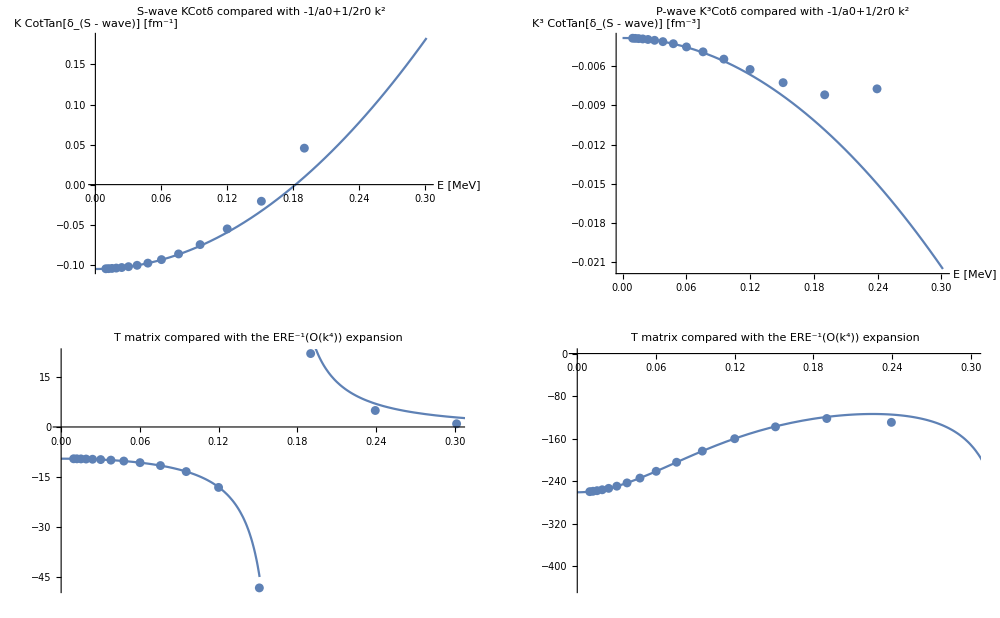

```mathematica
λλ=1;
mycore=core1;
rr=10;nGrid=100;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.01;
k0FMax=0.3;
Divisions=20;



(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;

(*---------------------*)
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2/4 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];
Print["Core = ",mycore]
ERE1=GetERE[mycore];
Print["ERE = ","     a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧]
PlotERE
```

λ = Λ^2/4 = 1.0000  ⇒ Λ = 2.0000 ; C_0 = -142.3630 ; D_0 = 173.9250

Core = {{-1.53,0.140094},{0.159045,0.662473},{1.58368,0.140094}}

ERE =      a0 = 9.99173     r0 = 6.68169     a1 = 332.259     r1 = -0.358492

S Pole Poitions in momentum: {-0.150691+0.152843 ⅈ,0.+0.18849 ⅈ,0.-0.494177 ⅈ,0.150691+0.152843 ⅈ}

S Pole Poitions in energy:   {-0.0180628-1.27355 ⅈ,-0.982266+0. ⅈ,-6.75177+0. ⅈ,-0.0180628+1.27355 ⅈ}

P Pole Poitions in momentum: {-0.184884+0.179227 ⅈ,0.-0.10093 ⅈ,0.+0.22214 ⅈ,0.184884+0.179227 ⅈ}

P Pole Poitions in energy:   {0.056947-1.83226 ⅈ,-0.28164+0. ⅈ,-1.36429+0. ⅈ,0.056947+1.83226 ⅈ}

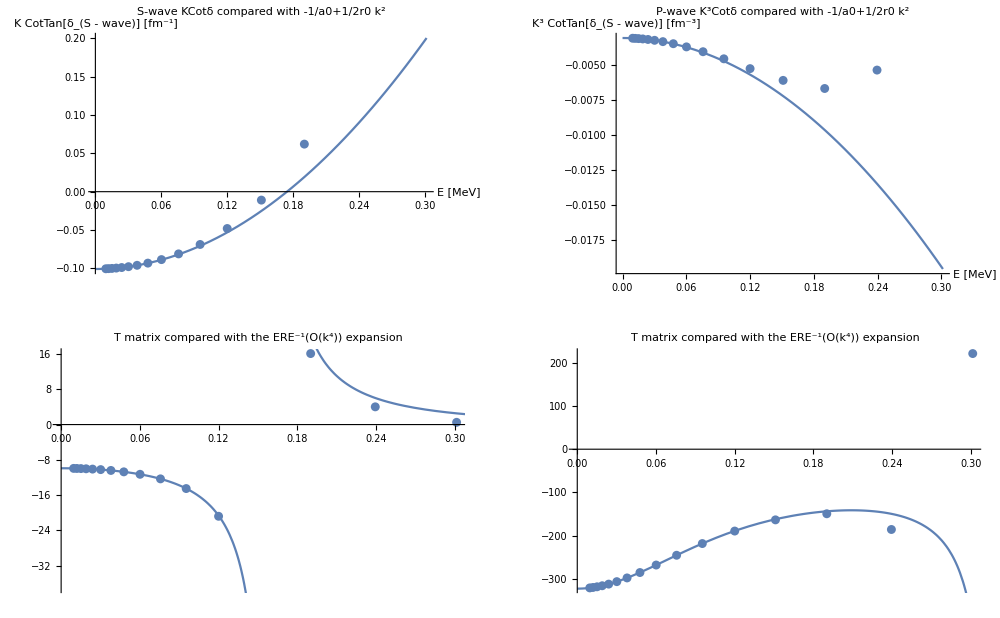

```mathematica
λλ=2;
mycore=core2;
rr=10;nGrid=100;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.01;
k0FMax=0.3;
Divisions=20;



(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;

(*---------------------*)
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2/4 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];
Print["Core = ",mycore]
ERE2=GetERE[mycore];
Print["ERE = ","     a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧]
PlotERE
```

λ = Λ^2/4 = 2.2500  ⇒ Λ = 3.0000 ; C_0 = -295.9300 ; D_0 = 566.6500

Core = {{-1.35096,0.162914},{0.189254,0.873276},{1.41418,0.162914}}

ERE =      a0 = 9.99173     r0 = 6.68169     a1 = 332.259     r1 = -0.358492

S Pole Poitions in momentum: {-0.149827+0.151872 ⅈ,0.+0.187277 ⅈ,0.-0.49102 ⅈ,0.149827+0.151872 ⅈ}

S Pole Poitions in energy:   {-0.0170547-1.2582 ⅈ,-0.969669+0. ⅈ,-6.66581+0. ⅈ,-0.0170547+1.2582 ⅈ}

P Pole Poitions in momentum: {-0.18349+0.177759 ⅈ,0.-0.100138 ⅈ,0.+0.22031 ⅈ,0.18349+0.177759 ⅈ}

P Pole Poitions in energy:   {0.0572318-1.80354 ⅈ,-0.277237+0. ⅈ,-1.3419+0. ⅈ,0.0572318+1.80354 ⅈ}

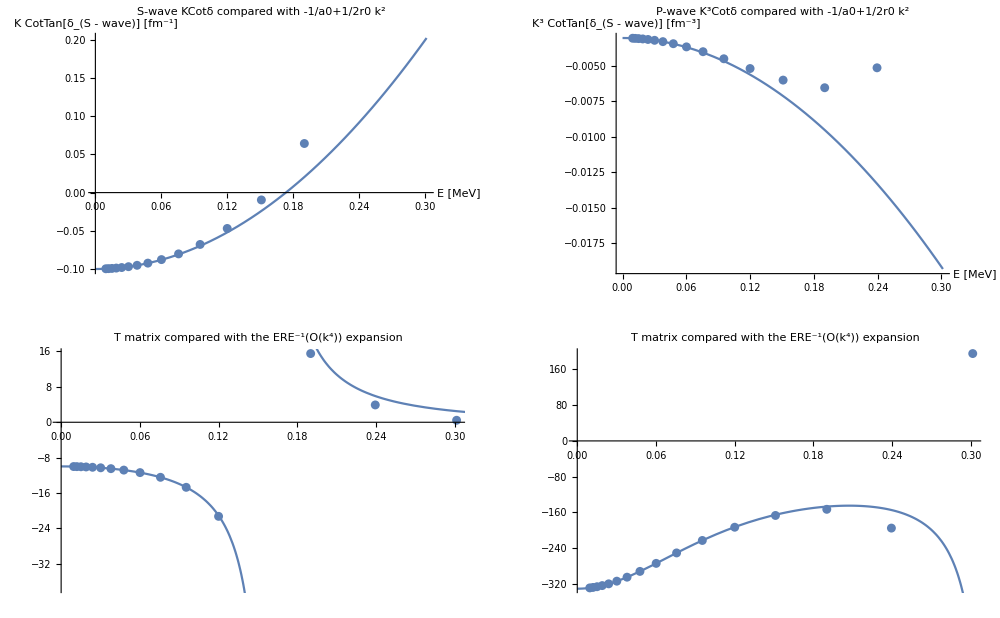

```mathematica
λλ=3;
mycore=core3;
rr=10;nGrid=100;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.01;
k0FMax=0.3;
Divisions=20;



(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;

(*---------------------*)
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2/4 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];
Print["Core = ",mycore]
ERE4=GetERE[mycore];
Print["ERE = ","     a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧]
PlotERE
```

```mathematica
λλ=4;
mycore=core4;
rr=10;nGrid=100;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.01;
k0FMax=0.3;
Divisions=20;



(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;

(*---------------------*)
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2/4 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];
Print["Core = ",mycore]
ERE3=GetERE[mycore];
Print["ERE = ","     a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧]
PlotERE
```

λ = Λ^2/4 = 4.0000  ⇒ Λ = 4.0000 ; C_0 = -505.1500 ; D_0 = 1426.7500

Core = {{-1.34759,0.178617},{0.208715,1.03031},{1.41757,0.178617}}

ERE =      a0 = 9.99173     r0 = 6.68169     a1 = 332.259     r1 = -0.358492

S Pole Poitions in momentum: {-0.14961+0.151628 ⅈ,0.+0.186973 ⅈ,0.-0.490229 ⅈ,0.14961+0.151628 ⅈ}

S Pole Poitions in energy:   {-0.0168032-1.25437 ⅈ,-0.966521+0. ⅈ,-6.64433+0. ⅈ,-0.0168032+1.25437 ⅈ}

P Pole Poitions in momentum: {-0.183152+0.177406 ⅈ,0.-0.0999462 ⅈ,0.+0.219867 ⅈ,0.183152+0.177406 ⅈ}

P Pole Poitions in energy:   {0.0572815-1.79664 ⅈ,-0.276176+0. ⅈ,-1.33651+0. ⅈ,0.0572815+1.79664 ⅈ}

-Graphics-

```mathematica
λλ=4;
mycore=core4;
rr=10;nGrid=100;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.01;
k0FMax=0.3;
Divisions=20;



(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;

(*---------------------*)
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2/4 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];
Print["Core = ",mycore]
ERE4=GetERE[mycore];
Print["ERE = ","     a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧]
PlotERE
```

λ = Λ^2/4 = 4.0000  ⇒ Λ = 4.0000 ; C_0 = -505.1500 ; D_0 = 1426.7500

Core = {{-1.34759,0.178617},{0.208715,1.03031},{1.41757,0.178617}}

ERE =      a0 = 9.99173     r0 = 6.68169     a1 = 332.259     r1 = -0.358492

S Pole Poitions in momentum: {-0.14961+0.151628 ⅈ,0.+0.186973 ⅈ,0.-0.490229 ⅈ,0.14961+0.151628 ⅈ}

S Pole Poitions in energy:   {-0.0168032-1.25437 ⅈ,-0.966521+0. ⅈ,-6.64433+0. ⅈ,-0.0168032+1.25437 ⅈ}

P Pole Poitions in momentum: {-0.183152+0.177406 ⅈ,0.-0.0999462 ⅈ,0.+0.219867 ⅈ,0.183152+0.177406 ⅈ}

P Pole Poitions in energy:   {0.0572815-1.79664 ⅈ,-0.276176+0. ⅈ,-1.33651+0. ⅈ,0.0572815+1.79664 ⅈ}

-Graphics-

λ = Λ^2/4 = 9.0000  ⇒ Λ = 6.0000 ; C_0 = -1090.5500 ; D_0 = 6552.5000

Core = {{-1.16434,0.198532},{0.232307,1.24303},{1.24292,0.198532}}

ERE =      a0 = 9.99173     r0 = 6.68169     a1 = 332.259     r1 = -0.358492

S Pole Poitions in momentum: {-0.149515+0.151521 ⅈ,0.+0.186839 ⅈ,0.-0.489881 ⅈ,0.149515+0.151521 ⅈ}

S Pole Poitions in energy:   {-0.0166928-1.25268 ⅈ,-0.965138+0. ⅈ,-6.63489+0. ⅈ,-0.0166928+1.25268 ⅈ}

P Pole Poitions in momentum: {-0.183001+0.177248 ⅈ,0.-0.0998604 ⅈ,0.+0.219669 ⅈ,0.183001+0.177248 ⅈ}

P Pole Poitions in energy:   {0.0573011-1.79356 ⅈ,-0.275702+0. ⅈ,-1.33411+0. ⅈ,0.0573011+1.79356 ⅈ}

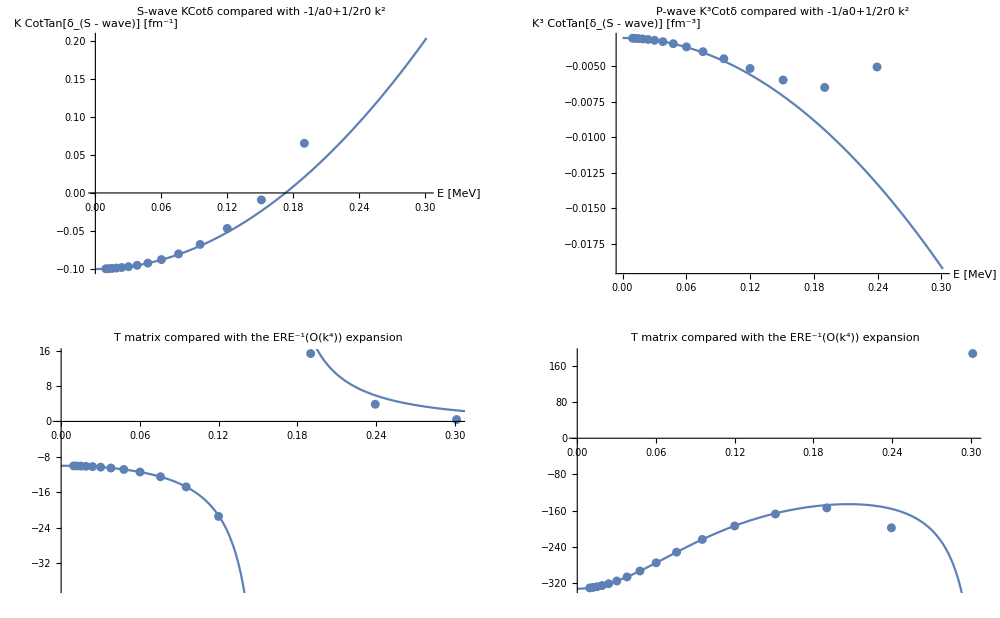

```mathematica
λλ=6;
mycore=core6;
rr=10;nGrid=100;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.01;
k0FMax=0.3;
Divisions=20;



(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;

(*---------------------*)
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2/4 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];
Print["Core = ",mycore]
ERE6=GetERE[mycore];
Print["ERE = ","     a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧]
PlotERE
```

λ = Λ^2/4 = 16.0000  ⇒ Λ = 8.0000 ; C_0 = -1898.5500 ; D_0 = 25697

Core = {{-1.14476,0.210204},{0.24585,1.37572},{1.22839,0.210204}}

ERE =      a0 = 9.99173     r0 = 6.68169     a1 = 332.259     r1 = -0.358492

S Pole Poitions in momentum: {-0.149499+0.151503 ⅈ,0.+0.186817 ⅈ,0.-0.489824 ⅈ,0.149499+0.151503 ⅈ}

S Pole Poitions in energy:   {-0.0166747-1.2524 ⅈ,-0.964912+0. ⅈ,-6.63335+0. ⅈ,-0.0166747+1.2524 ⅈ}

P Pole Poitions in momentum: {-0.182975+0.177221 ⅈ,0.-0.0998458 ⅈ,0.+0.219635 ⅈ,0.182975+0.177221 ⅈ}

P Pole Poitions in energy:   {0.0573042-1.79304 ⅈ,-0.275621+0. ⅈ,-1.3337+0. ⅈ,0.0573042+1.79304 ⅈ}

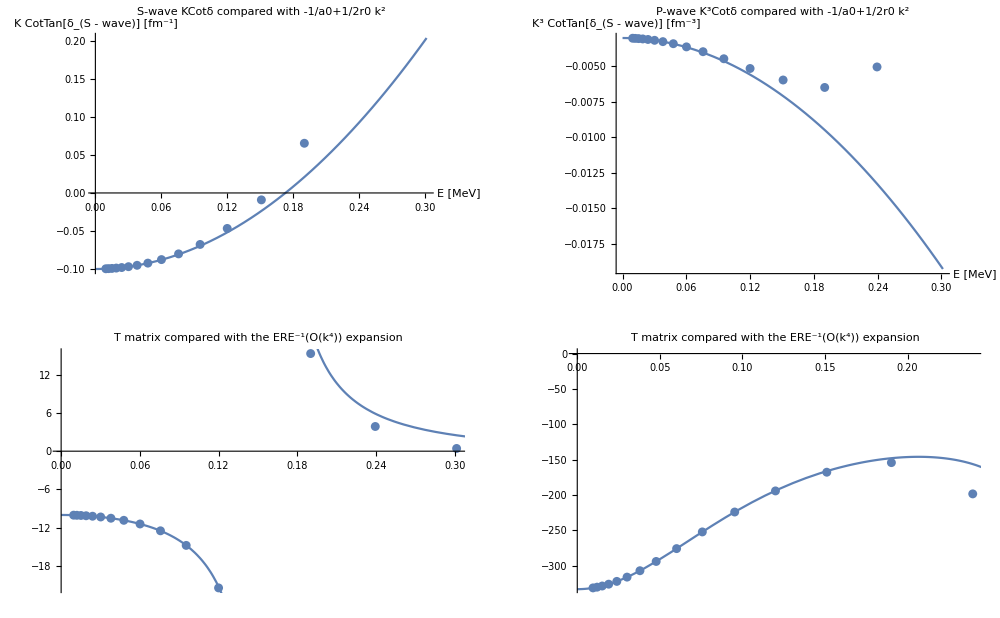

```mathematica
λλ=8;
mycore=core8;
rr=10;nGrid=100;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.01;
k0FMax=0.3;
Divisions=20;



(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;

(*---------------------*)
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2/4 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];
Print["Core = ",mycore]
ERE8=GetERE[mycore];
Print["ERE = ","     a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧]
PlotERE
```

λ = Λ^2/4 = 25.0000  ⇒ Λ = 10.0000 ; C_0 = -2929.1700 ; D_0 = 92495

Core = {{-1.12811,0.221642},{0.257821,1.49207},{1.21622,0.221642}}

ERE =      a0 = 9.99173     r0 = 6.68169     a1 = 332.259     r1 = -0.358492

S Pole Poitions in momentum: {-0.149495+0.151498 ⅈ,0.+0.186811 ⅈ,0.-0.489808 ⅈ,0.149495+0.151498 ⅈ}

S Pole Poitions in energy:   {-0.0166697-1.25233 ⅈ,-0.964848+0. ⅈ,-6.63292+0. ⅈ,-0.0166697+1.25233 ⅈ}

P Pole Poitions in momentum: {-0.182967+0.177213 ⅈ,0.-0.0998415 ⅈ,0.+0.219625 ⅈ,0.182967+0.177213 ⅈ}

P Pole Poitions in energy:   {0.0573051-1.79288 ⅈ,-0.275598+0. ⅈ,-1.33358+0. ⅈ,0.0573051+1.79288 ⅈ}

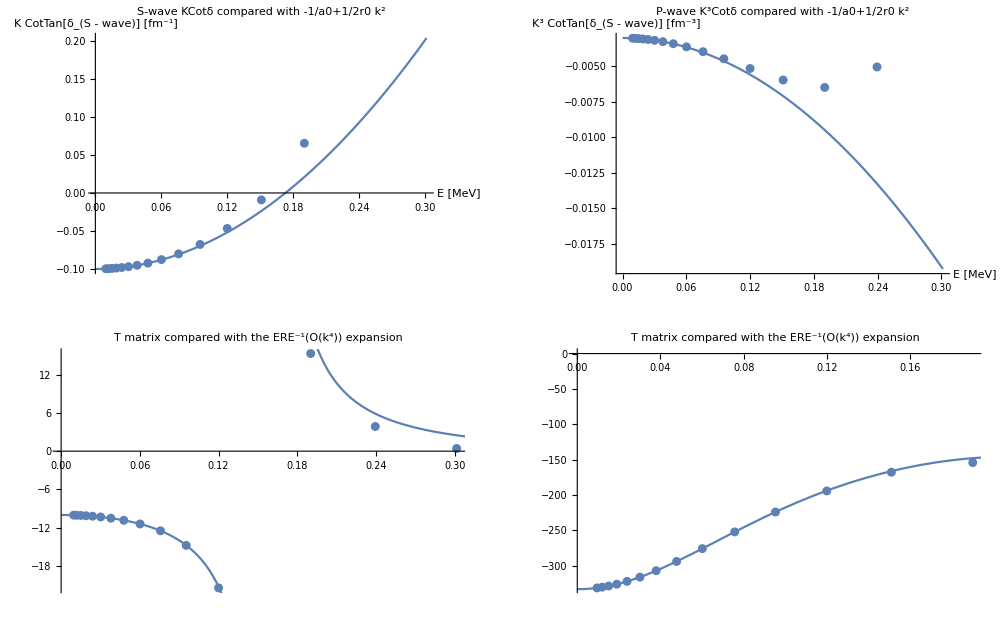

```mathematica
λλ=10;
mycore=core10;
rr=10;nGrid=100;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.01;
k0FMax=0.3;
Divisions=20;



(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;

(*---------------------*)
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2/4 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];
Print["Core = ",mycore]
ERE10=GetERE[mycore];
Print["ERE = ","     a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧]
PlotERE
```

## Fit the core from the ERE parameters

```mathematica
(* I need a simple function to contain the fit*)
FitEre[x_?(VectorQ[#, NumericQ]&)]:=Module[{Aa0=x[[1]],Cc1=x[[2]],Aa1=x[[3]]},
mycore={{1.,Aa0},{Cc1,Aa1}};
ERE=GetERE[mycore];
a0tf=ERE⟦1⟧;
r0tf=ERE⟦2⟧;
a1tf=ERE⟦3⟧;
iIi=iIi+1;
Print["iter: ", iIi, "       core={1, ",Aa0,", ",Cc1,", ", Aa1"}     |     ERE = ", ERE  , "     |    to goal: ", {a0tf^-1,r0tf,a1tf^-1}-Goal ];
{a0tf^-1,r0tf,a1tf^-1}-Goal
]
```

λ = Λ^2/4 = 4.0000  ⇒ Λ = 4.0000 ; C_0 = -505.1500 ; D_0 = 1426.7500

Core = {{-1.34759,0.178617},{0.208715,1.03031},{1.41757,0.178617}}

ERE =      a0 = 9.99847     r0 = 6.84093     a1 = 333.18     r1 = -0.344261

S Pole Poitions in momentum: {-0.158053+0.128757 ⅈ,0.+0.161528 ⅈ,0.-0.419043 ⅈ,0.158053+0.128757 ⅈ}

S Pole Poitions in energy:   {0.232299-1.12527 ⅈ,-0.721359+0. ⅈ,-4.85479+0. ⅈ,0.232299+1.12527 ⅈ}

P Pole Poitions in momentum: {-0.194228+0.162926 ⅈ,0.-0.0994097 ⅈ,0.+0.200429 ⅈ,0.194228+0.162926 ⅈ}

P Pole Poitions in energy:   {0.309088-1.7498 ⅈ,-0.273219+0. ⅈ,-1.11065+0. ⅈ,0.309088+1.7498 ⅈ}

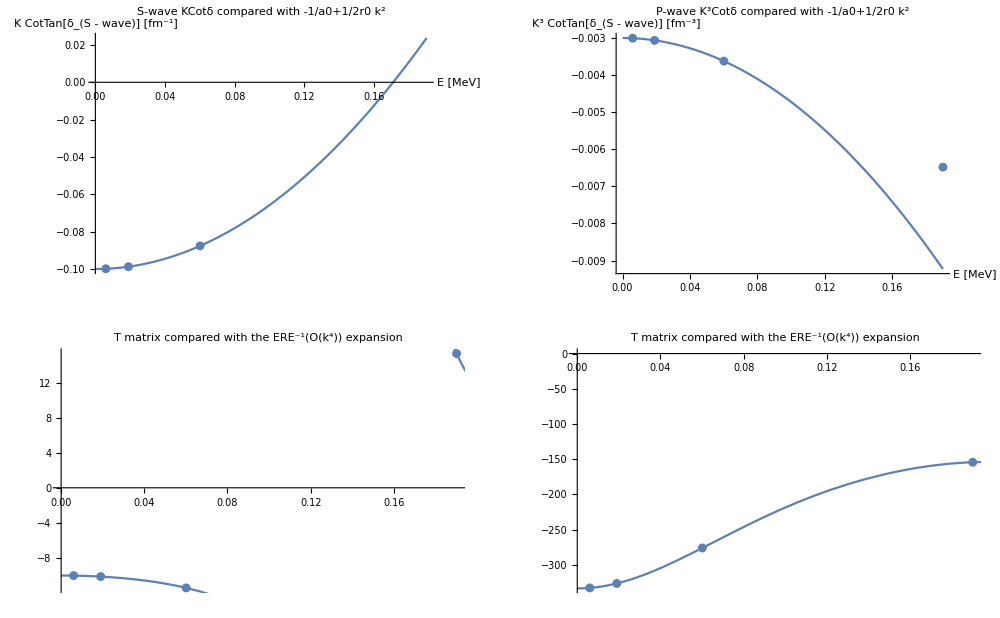

```mathematica
(*Go with the fit*)
λλ=4;
mycore=core4;
rr=10;nGrid=20;
f1=1;f2=3; 

k0FMin=0.01;
k0FMax=0.1;
Divisions=3;



(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;

(*--------- Test that all is ok------------*)
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2/4 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];
Print["Core = ",mycore]
ERE=GetERE[mycore];
Print["ERE = ","     a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧]
PlotERE
```

```mathematica
nk=2;
core={}; Do[core=AppendTo[core,ToExpression@Map[StringJoin[#,ToString[k]]&,{"C","Α"}]],{k,1,nk}];
wf=Total[Flatten[Table[core⟦i⟧⟦1⟧ⅇ^(-core⟦i⟧⟦2⟧ r^2) ,{i,Length[core]}]]];

core4f=core/.FindFit[Mϕ4,wf,corefit,r];
wf4f   =Total[Flatten[Table[core4⟦i⟧⟦1⟧ⅇ^(-core4⟦i⟧⟦2⟧ r^2) ,{i,Length[core4]}]]];
core6f=core/.FindFit[Mϕ6,wf,corefit,r];
wf6f   =Total[Flatten[Table[core6⟦i⟧⟦1⟧ⅇ^(-core6⟦i⟧⟦2⟧ r^2) ,{i,Length[core6]}]]];

Print["wf4 = ", wf4f]
Print["wf6 = ", wf6f]
```

wf4 = 0.208715 ⅇ^(-1.03031 r^2)-1.34759 ⅇ^(-0.178617 r^2)+1.41757 ⅇ^(-0.178617 r^2)

wf6 = 0.232307 ⅇ^(-1.24303 r^2)+1.24292 ⅇ^(-0.198532 r^2)-1.16434 ⅇ^(-0.198532 r^2)

```mathematica
(*--------run fit---------*)
iIi=0;
xini=Flatten[wf4f]
Goal={3.32^-1, 2.55,-20.23^-1};
CoreFitted4=FindRoot[FitEre[x],{x,xini},PrecisionGoal->4,AccuracyGoal->4]
```

0.208715 ⅇ^(-1.03031 r^2)-1.34759 ⅇ^(-0.178617 r^2)+1.41757 ⅇ^(-0.178617 r^2)

FindRoot::srect: Value 0.208715 ⅇ^(-1.03031 r^2)-1.34759 ⅇ^(-0.178617 r^2)+1.41757 ⅇ^(-0.178617 r^2) in search specification {x,xini} is not a number or array of numbers.

FindRoot[FitEre[x],{x,xini},PrecisionGoal→4,AccuracyGoal→4]

λ = Λ^2/4 = 9.0000  ⇒ Λ = 6.0000 ; C_0 = -1090.5500 ; D_0 = 6552.5000

Core = {{-1.16434,0.198532},{0.232307,1.24303},{1.24292,0.198532}}

ERE =      a0 = 9.99847     r0 = 6.84093     a1 = 333.181     r1 = -0.34426

S Pole Poitions in momentum: {-0.158053+0.128757 ⅈ,0.+0.161528 ⅈ,0.-0.419043 ⅈ,0.158053+0.128757 ⅈ}

S Pole Poitions in energy:   {0.232299-1.12527 ⅈ,-0.721359+0. ⅈ,-4.85478+0. ⅈ,0.232299+1.12527 ⅈ}

P Pole Poitions in momentum: {-0.194228+0.162926 ⅈ,0.-0.0994096 ⅈ,0.+0.200429 ⅈ,0.194228+0.162926 ⅈ}

P Pole Poitions in energy:   {0.309088-1.74979 ⅈ,-0.273218+0. ⅈ,-1.11064+0. ⅈ,0.309088+1.74979 ⅈ}

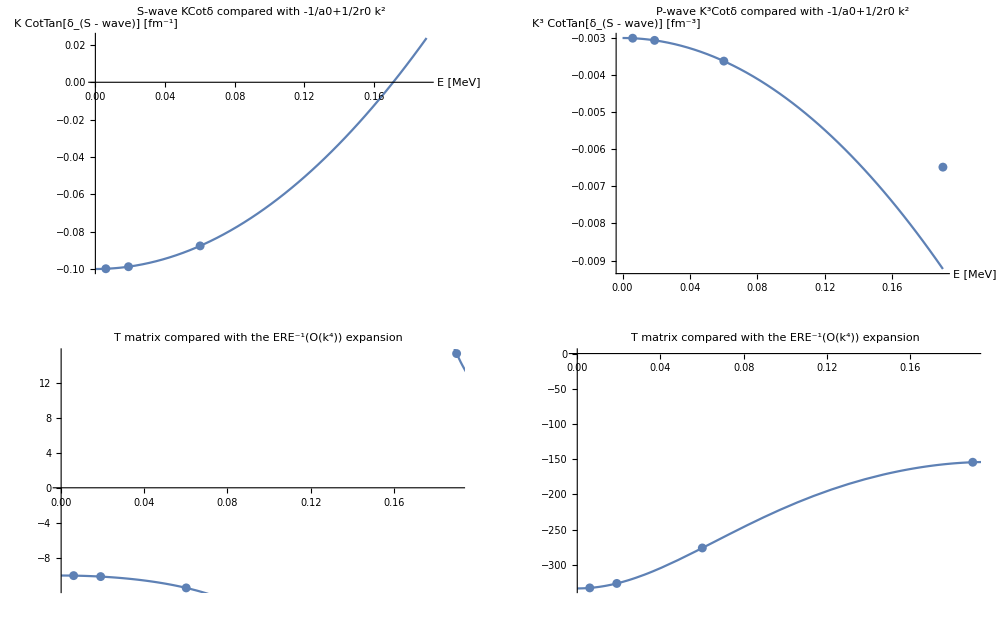

```mathematica
(*Go with the fit*)
λλ=6;
mycore=core6;
rr=10;nGrid=20;
f1=1;f2=3; 

k0FMin=0.01;
k0FMax=0.1;
Divisions=3;



(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;

(*--------- Test that all is ok------------*)
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2/4 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];
Print["Core = ",mycore]
ERE=GetERE[mycore];
Print["ERE = ","     a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧]
PlotERE
```

```mathematica
(*--------run fit---------*)
iIi=0;
xini==Flatten[wf6f]
Goal={3.32^-1, 2.55,-20.23^-1};
CoreFitted6=FindRoot[FitEre[x],{x,xini},PrecisionGoal->4,AccuracyGoal->4]
```

0.208715 ⅇ^(-1.03031 r^2)-1.34759 ⅇ^(-0.178617 r^2)+1.41757 ⅇ^(-0.178617 r^2)==0.232307 ⅇ^(-1.24303 r^2)+1.24292 ⅇ^(-0.198532 r^2)-1.16434 ⅇ^(-0.198532 r^2)

FindRoot::srect: Value 0.208715 ⅇ^(-1.03031 r^2)-1.34759 ⅇ^(-0.178617 r^2)+1.41757 ⅇ^(-0.178617 r^2) in search specification {x,xini} is not a number or array of numbers.

FindRoot[FitEre[x],{x,xini},PrecisionGoal→4,AccuracyGoal→4]